```mathematica
A=Select[Map[Partition[#,2]&,Permutations[Range[6]]],Total[#[[1]]]==7&&Total[#[[2]]]==7&];
```

```mathematica
For[k=1,k≤48,k++,
B=A[[k]];
Print[B];
flag=False;
For[t=2,t<100,t++,
If[flag,Break[]];
For[i=1,i≤t/2,i++,
j=t-i;
top=B[[1,1]]j-B[[3,1]]i;
bottom=B[[1,2]]j-B[[3,2]]i;
BB=Map[Total,Transpose[B]];
If[IntegerQ[top/BB[[1]]]&&IntegerQ[bottom/BB[[2]]]&&top=!=0&&bottom=!=0,Print[t,": ",i," ",j];flag=True;]]]]
```

5: 1 4

{{5,2},{3,4},{6,1}}

5: 1 4

{{5,2},{4,3},{1,6}}

```mathematica
A=Permutations[Range[7]];
```

```mathematica
For[k=1,k≤5040,k++,
B=A[[k]];
flag=False;
For[tt=21,tt≤24,tt++,
For[t1=2,t1≤tt-2,t1++,
t2=tt-t1;
For[i1=1,i1≤t1-1,i1++,
j1=t1-i1;
If[Mod[B[[1]]i1,B[[1]]+B[[2]]]==0&&Mod[B[[3]]i1-B[[5]]j1,B[[3]]+B[[4]]+B[[5]]]==0&&Mod[-B[[7]]j1,B[[6]]+B[[7]]]==0&&B[[3]]i1-B[[5]]j1=!=0,
For[i2=1,i2≤t2-1,i2++,
j2=t2-i2;
If[Mod[B[[1]]i2,B[[1]]+B[[3]]]==0&&Mod[B[[2]]i2-B[[6]]j2,B[[2]]+B[[4]]+B[[6]]]==0&&Mod[-B[[7]]j2,B[[5]]+B[[7]]]==0&&B[[2]]i2-B[[6]]j2=!=0,Print[B," ",tt,": ",i1," ",j1," ",i2," ",j2];flag=True;]]]]];
If[flag,tt=31]]];
```

{1,2,5,7,3,6,4} 24: 6 5 6 7

{1,5,2,7,6,3,4} 24: 6 7 6 5

{4,3,6,7,2,5,1} 24: 7 6 5 6

{4,6,3,7,5,2,1} 24: 5 6 7 6

```mathematica
For[k=1,k≤5040,k++,
B=A[[k]];
flag=False;
For[tt=4,tt≤24,tt++,
For[t1=2,t1≤tt-2,t1++,
t2=tt-t1;
For[i1=1,i1≤t1-1,i1++,
j1=t1-i1;
If[Mod[B[[1]]i1-B[[3]]j1,B[[1]]+B[[2]]+B[[3]]]==0&&Mod[B[[4]]i1,B[[4]]+B[[5]]]==0&&Mod[-B[[7]]j1,B[[6]]+B[[7]]]==0&&B[[1]]i1-B[[3]]j1=!=0,
For[i2=1,i2≤t2-1,i2++,
j2=t2-i2;
If[Mod[B[[1]]i2,B[[1]]+B[[4]]]==0&&Mod[B[[2]]i2-B[[6]]j2,B[[2]]+B[[5]]+B[[6]]]==0&&Mod[B[[3]]i2-B[[7]]j2,B[[3]]+B[[7]]]==0&&B[[2]]i2-B[[6]]j2=!=0,Print[B," ",tt,": ",i1," ",j1," ",i2," ",j2];flag=True;]]]]];
If[flag,tt=25]]];
```

{2,7,6,1,5,3,4} 18: 6 7 3 2

```mathematica
For[k=1,k≤5040,k++,
B=A[[k]];
flag=False;
For[tt=14,tt≤18,tt++,
For[t1=2,t1≤tt-2,t1++,
t2=tt-t1;
For[i1=1,i1≤t1-1,i1++,
j1=t1-i1;
If[Mod[B[[1]]i1-B[[3]]j1,B[[1]]+B[[2]]+B[[3]]]==0&&Mod[B[[4]]i1-B[[5]]j1,B[[4]]+B[[5]]]==0&&Mod[-B[[7]]j1,B[[6]]+B[[7]]]==0&&B[[1]]i1-B[[3]]j1=!=0,
For[i2=1,i2≤t2-1,i2++,
j2=t2-i2;
If[Mod[B[[1]]i2,B[[1]]+B[[4]]]==0&&Mod[B[[2]]i2-B[[6]]j2,B[[2]]+B[[6]]]==0&&Mod[B[[3]]i2-B[[7]]j2,B[[3]]+B[[5]]+B[[7]]]==0&&B[[3]]i2-B[[7]]j2=!=0,Print[B," ",tt,": ",i1," ",j1," ",i2," ",j2];flag=True;]]]]];
If[flag,tt=25]]];
```

{1,2,7,3,6,4,5} 18: 3 9 4 2

{1,3,7,2,5,4,6} 14: 2 5 6 1

{5,6,7,4,2,3,1} 18: 2 4 9 3

{6,5,7,4,3,2,1} 14: 1 6 5 2

```mathematica
For[k=1,k≤5040,k++,
B=A[[k]];
flag=False;
For[tt=14,tt≤18,tt++,
For[t1=2,t1≤tt-2,t1++,
t2=tt-t1;
For[i1=1,i1≤t1-1,i1++,
j1=t1-i1;
If[Mod[B[[1]]i1-B[[3]]j1,B[[1]]+B[[2]]+B[[3]]]==0&&Mod[B[[4]]i1,B[[4]]+B[[5]]]==0&&Mod[B[[6]]i1-B[[7]]j1,B[[6]]+B[[7]]]==0&&B[[1]]i1-B[[3]]j1=!=0,
For[i2=1,i2≤t2-1,i2++,
j2=t2-i2;
If[Mod[B[[1]]i2-B[[6]]j2,B[[1]]+B[[4]]+B[[6]]]==0&&Mod[B[[2]]i2,B[[2]]+B[[5]]]==0&&Mod[B[[3]]i2-B[[7]]j2,B[[3]]+B[[7]]]==0&&B[[1]]i2-B[[6]]j2=!=0,Print[B," ",tt,": ",i1," ",j1," ",i2," ",j2];flag=True;]]]]];
If[flag,tt=25]]];
```

{7,1,5,6,2,4,3} 15: 4 3 6 2

{7,6,4,1,2,5,3} 15: 6 2 4 3

```mathematica
A=Select[Map[Partition[#,2]&,Permutations[Range[8]]],Total[#[[1]]]==9&&Total[#[[2]]]==9&&Total[#[[3]]]==9&&MemberQ[#[[{1,2},1]],1]&];
```

```mathematica
For[t=4,t≤4,t++,Print["t=",t];
For[k=1,k≤96,k++,
B=A[[k]];
For[i=1,i≤t-2,i++,
For[j=1,j≤t-i-1,j++,
m=t-i-j;
top=B[[1,1]]i-B[[3,1]]j-B[[4,1]](j+m);
bottom=B[[1,2]]i-B[[3,2]]j-B[[4,2]](j+m);
BB=Map[Total,Transpose[B]];
If[IntegerQ[top/BB[[1]]]&&IntegerQ[bottom/BB[[2]]]&&top=!=0&&bottom=!=0&&top=!=BB[[1]]j&&bottom=!= BB[[2]]j,Print[B," ",t,": ",i," ",j," ",m]]]]]]
```

t=4

{{1,8},{5,4},{3,6},{2,7}} 4: 1 2 1

{{1,8},{6,3},{4,5},{2,7}} 4: 1 2 1

```mathematica
A=Select[Permutations[Range[8]],#[[3]]<#[[7]]&];
```

```mathematica
Length[A]
```

20160

```mathematica
For[k=1,k≤20160,k++,
B=A[[k]];
flag=False;
For[tt=6,tt≤16,tt++,
For[t1=2,t1≤tt-2,t1++,
t2=tt-t1;
For[i1=1,i1≤t1-1,i1++,
j1=t1-i1;
If[Mod[B[[1]]i1-B[[3]]j1,B[[1]]+B[[2]]+B[[3]]]==0&&Mod[B[[4]]i1-B[[6]]j1,B[[4]]+B[[5]]+B[[6]]]==0&&Mod[B[[7]]i1,B[[7]]+B[[8]]]==0&&B[[1]]i1-B[[3]]j1=!=0&&B[[4]]i1-B[[6]]j1=!=0,
For[i2=1,i2≤t2-1,i2++,
j2=t2-i2;
If[Mod[B[[1]]i2-B[[7]]j2,B[[1]]+B[[4]]+B[[7]]]==0&&Mod[B[[2]]i2-B[[8]]j2,B[[2]]+B[[5]]+B[[8]]]==0&&Mod[B[[3]]i2,B[[3]]+B[[6]]]==0&&B[[1]]i2-B[[7]]j2=!=0&&B[[2]]i2-B[[8]]j2=!=0,Print[B," ",tt,": ",i1," ",j1," ",i2," ",j2];flag=True;]]]]];
If[flag,tt=25]]];
```

{3,7,2,1,5,6,4,8} 14: 6 3 4 1

{5,6,1,7,2,3,4,8} 11: 3 3 4 1

{6,5,1,2,7,3,8,4} 14: 3 6 4 1

{7,2,3,5,6,1,4,8} 13: 3 3 4 3

{7,3,2,5,1,6,8,4} 14: 6 3 4 1

{7,8,1,6,4,3,5,2} 14: 7 1 4 2

```mathematica
For[k=1,k≤20160,k++,
B=A[[k]];
flag=False;
For[tt=6,tt≤16,tt++,
For[t1=2,t1≤tt-2,t1++,
t2=tt-t1;
For[i1=1,i1≤t1-1,i1++,
j1=t1-i1;
If[Mod[B[[1]]i1-B[[3]]j1,B[[1]]+B[[2]]+B[[3]]]==0&&Mod[B[[4]]i1-B[[6]]j1,B[[4]]+B[[5]]+B[[6]]]==0&&Mod[B[[7]]i1-B[[8]]j1,B[[7]]+B[[8]]]==0&&B[[1]]i1-B[[3]]j1=!=0&&B[[4]]i1-B[[6]]j1=!=0,
For[i2=1,i2≤t2-1,i2++,
j2=t2-i2;
If[Mod[B[[1]]i2-B[[7]]j2,B[[1]]+B[[4]]+B[[7]]]==0&&Mod[B[[2]]i2,B[[2]]+B[[5]]]==0&&Mod[B[[3]]i2-B[[8]]j2,B[[3]]+B[[6]]+B[[8]]]==0&&B[[1]]i2-B[[7]]j2=!=0&&B[[3]]i2-B[[8]]j2=!=0,Print[B," ",tt,": ",i1," ",j1," ",i2," ",j2];flag=True;]]]]];
If[flag,tt=25]]];
```

{3,2,7,1,6,5,8,4} 13: 3 3 4 3

{3,4,5,2,8,6,7,1} 14: 2 6 3 3

{3,6,7,1,2,5,8,4} 13: 1 5 4 3

{3,8,5,2,4,6,7,1} 14: 3 5 3 3

{6,1,5,2,3,7,8,4} 14: 3 6 4 1

{7,2,3,5,6,1,4,8} 13: 3 3 4 3

{7,2,3,5,6,1,8,4} 11: 3 3 4 1

{7,4,1,2,8,6,3,5} 14: 4 4 3 3

{7,6,3,5,2,1,4,8} 13: 5 1 4 3

{7,6,3,5,2,1,8,4} 11: 5 1 4 1

{7,8,1,2,4,6,3,5} 14: 3 5 3 3

```mathematica
For[k=1,k≤20160,k++,
B=A[[k]];
flag=False;
For[tt=6,tt≤16,tt++,
For[t1=2,t1≤tt-2,t1++,
t2=tt-t1;
For[i1=1,i1≤t1-1,i1++,
j1=t1-i1;
If[Mod[B[[1]]i1-B[[3]]j1,B[[1]]+B[[2]]+B[[3]]]==0&&Mod[B[[4]]i1-B[[5]]j1,B[[4]]+B[[5]]]==0&&Mod[B[[6]]i1-B[[8]]j1,B[[7]]+B[[8]]+B[[6]]]==0&&B[[1]]i1-B[[3]]j1=!=0&&B[[6]]i1-B[[8]]j1=!=0,
For[i2=1,i2≤t2-1,i2++,
j2=t2-i2;
If[Mod[B[[1]]i2-B[[6]]j2,B[[1]]+B[[4]]+B[[6]]]==0&&Mod[B[[2]]i2-B[[7]]j2,B[[2]]+B[[7]]]==0&&Mod[B[[3]]i2-B[[8]]j2,B[[3]]+B[[5]]+B[[8]]]==0&&B[[1]]i2-B[[6]]j2=!=0&&B[[3]]i2-B[[8]]j2=!=0,Print[B," ",tt,": ",i1," ",j1," ",i2," ",j2];flag=True;]]]]];
If[flag,tt=25]]];
```

{1,3,2,5,4,7,6,8} 12: 2 7 1 2

{2,3,1,4,5,8,6,7} 12: 7 2 1 2

{5,1,2,4,8,7,3,6} 10: 4 2 1 3

{5,4,7,1,3,2,8,6} 10: 1 3 4 2

{6,8,2,3,1,7,4,5} 10: 3 1 2 4

{7,4,5,3,1,6,8,2} 10: 3 1 4 2

{7,5,1,6,3,8,4,2} 12: 2 1 2 7

{8,4,2,6,3,7,5,1} 12: 2 1 7 2

```mathematica
te[n_,x_,y_]:=If[n=="■",Text[Style[n,FontSize->14],{x-1/2,y-1/2}],Text[Style[n,FontSize->14],{x-1/2,y-.55}]]
```

## 6

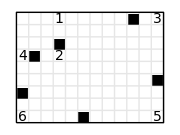

```mathematica
x=12;y=9;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[6,1,1],te[4,1,6],te[5,12,1],te[3,12,9],te[1,4,9],te[2,4,6],te["■",6,1],te["■",1,3],te["■",2,6],te["■",4,7],te["■",10,9],te["■",12,4]},ImageSize->15{x,y}]
```

## 7

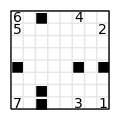

```mathematica
x=8;y=8;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[1,8,1],te[3,6,1],te[7,1,1],te[5,1,7],te[2,8,7],te[6,1,8],te[4,6,8],te["■",3,1],te["■",3,2],te["■",3,8],te["■",1,4],te["■",6,4],te["■",8,4]},ImageSize->15{x,y}]
```

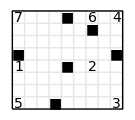

```mathematica
x=9;y=8;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[7,1,8],te[6,7,8],te[4,9,8],te[1,1,4],te[2,7,4],te[5,1,1],te[3,9,1],te["■",9,5],te["■",7,7],te["■",1,5],te["■",4,1],te["■",5,4],te["■",5,8]},ImageSize->15{x,y}]
```

```mathematica
x=14;y=6;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[2,1,6],te[7,7,6],te[6,14,6],te[1,1,3],te[5,7,3],te[3,7,1],te[4,14,1],te["■",1,4],te["■",14,4],te["■",7,4],te["■",10,1],te["■",6,3],te["■",9,6]},ImageSize->15{x,y}]
```

-Graphics-

## 8

```mathematica
x=10;y=5;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[1,1,5],te[5,1,4],te[3,1,2],te[2,1,1],te[8,10,5],te[4,10,4],te[6,10,2],te[7,10,1],te["■",1,3],te["■",10,3],te["■",8,1],te["■",7,2],te["■",9,5],te["■",5,4]},ImageSize->15{x,y}]
```

-Graphics-

```mathematica
x=7;y=6;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[8,4,6],te[4,7,6],te[3,1,5],te[2,4,5],te[7,7,5],te[1,1,1],te[6,4,1],te[5,7,1],te["■",5,1],te["■",5,5],te["■",5,6],te["■",1,4],te["■",4,4],te["■",7,4]},ImageSize->10{x,y}]
```

-Graphics-

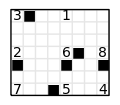

```mathematica
x=8;y=7;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[7,1,1],te[2,1,4],te[3,1,7],te[5,5,1],te[6,5,4],te[1,5,7],te[4,8,1],te[8,8,4],te["■",8,3],te["■",5,3],te["■",1,3],te["■",4,1],te["■",6,4],te["■",2,7]},ImageSize->15{x,y}]
```

```mathematica
x=10;y=6;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[7,1,6],te[3,7,6],te[2,10,6],te[5,1,2],te[1,7,2],te[6,10,2],te[8,1,1],te[4,7,1],te["■",7,3],te["■",10,3],te["■",1,3],te["■",3,1],te["■",6,2],te["■",4,6]},ImageSize->15{x,y}]
```

-Graphics-

```mathematica
x=7;y=6;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[7,1,6],te[2,4,6],te[3,7,6],te[5,1,2],te[6,4,2],te[1,7,2],te[8,1,1],te[4,7,1],te["■",7,3],te["■",4,3],te["■",1,3],te["■",3,1],te["■",3,2],te["■",3,6]},ImageSize->15{x,y}]
```

-Graphics-

```mathematica
x=7;y=6;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[7,7,1],te[6,2,1],te[3,1,1],te[5,7,5],te[2,2,5],te[1,1,5],te[8,7,6],te[4,1,6],te["■",7,4],te["■",2,2],te["■",1,4],te["■",4,1],te["■",5,5],te["■",5,6]},ImageSize->15{x,y}]
```

-Graphics-

```mathematica
x=7;y=5;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[5,1,5],te[1,5,5],te[2,7,5],te[4,1,4],te[8,7,4],te[7,1,1],te[3,5,1],te[6,7,1],te["■",7,3],te["■",4,5],te["■",1,3],te["■",4,1],te["■",5,2],te["■",5,4]},ImageSize->15{x,y}]
```

-Graphics-

```mathematica
x=10;y=4;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[8,1,1],te[4,1,3],te[2,1,4],te[6,8,1],te[3,8,4],te[7,10,1],te[5,10,3],te[1,10,4],te["■",10,2],te["■",8,2],te["■",1,2],te["■",6,1],te["■",6,4],te["■",6,3]},ImageSize->15{x,y}]
```

-Graphics-

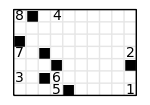

```mathematica
x=10;y=7;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],
te[3,1,2],te[7,1,4],te[8,1,7],te[5,4,1],te[6,4,2],te[4,4,7],te[1,10,1],te[2,10,4],
te["■",5,1],te["■",3,2],te["■",10,3],te["■",1,5],te["■",2,7],te["■",4,3],te["■",3,4]},ImageSize->15{x,y}]
```

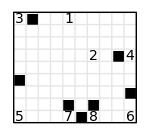

```mathematica
x=10;y=9;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],
te[5,1,1],te[7,5,1],te[8,7,1],te[6,10,1],te[3,1,9],te[1,5,9],te[2,7,6],te[4,10,6],
te["■",6,1],te["■",1,4],te["■",5,2],te["■",7,2],te["■",10,3],te["■",9,6],te["■",2,9]},ImageSize->15{x,y}]
```

```mathematica
f[x_,y_]:=(x+y)/GCD[x,y]
```

```mathematica
g[L_]:=(f[L[[1]],L[[2]]]+f[L[[5]],L[[6]]]==f[L[[3]],L[[4]]]+f[L[[7]],L[[8]]])&&(f[L[[2]],L[[3]]]+f[L[[6]],L[[7]]]==f[L[[4]],L[[5]]]+f[L[[8]],L[[1]]])
```

```mathematica
Select[Permutations[Range[8]],#[[2]]==7&&#[[1]]<#[[3]]&&g[#]&]
```

```mathematica
{{4,7,8,5,6,1,2,3}}
```

## 9

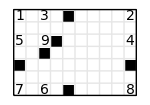

```mathematica
Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,7}}],{i,1,9}],Table[Line[{{0,i},{10,i}}],{i,1,6}],Black,Line[{{0,0},{10,0},{10,7},{0,7},{0,0}}],te[1,1,7],te[3,3,7],te[2,10,7],te[5,1,5],te[9,3,5],te[4,10,5],te[7,1,1],te[6,3,1],te[8,10,1],te["■",5,1],te["■",5,7],te["■",4,5],te["■",1,3],te["■",10,3],te["■",3,4]},ImageSize->15{10,7}]
```

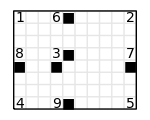

```mathematica
x=10;y=8;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[1,1,8],te[6,4,8],te[2,10,8],te[8,1,5],te[3,4,5],te[7,10,5],te[4,1,1],te[9,4,1],te[5,10,1],te["■",5,1],te["■",5,5],te["■",5,8],te["■",1,4],te["■",4,4],te["■",10,4]},ImageSize->15{x,y}]
```

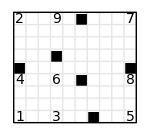

```mathematica
x=10;y=9;Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],te[1,1,1],te[4,1,4],te[2,1,9],te[3,4,1],te[6,4,4],te[9,4,9],te[5,10,1],te[8,10,4],te[7,10,9],te["■",1,5],te["■",4,6],te["■",10,5],te["■",7,1],te["■",6,4],te["■",6,9]},ImageSize->15{x,y}]
```

```mathematica
f[L_,xx_,yy_,zz_,aa_,bb_]:=Module[{x,y},
y=xx+yy+zz+1;x=aa+bb+1;
hd={0,xx,xx+yy,xx+yy+zz};
vd={0,aa,aa+bb};Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],
MapIndexed[If[#1>0,te[#1,1+vd[[#2[[1]]]],1+hd[[#2[[2]]]]],{}]&,L,{2}],
MapIndexed[te["■",1+vd[[#2[[1]]]],1+#1.hd/Total[#1]]&,L,1],
MapIndexed[te["■",1+#1.vd/Total[#1],1+hd[[#2[[1]]]]]&,Transpose[L],1]
},ImageSize->15{x,y}]]
```

```mathematica
ff[L_,xx_,yy_,zz_,aa_,bb_]:=Module[{x,y},
x=xx+yy+zz+1;y=aa+bb+1;
hd={0,xx,xx+yy,xx+yy+zz};
vd={0,aa,aa+bb};Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,y}}],{i,1,x}],Table[Line[{{0,i},{x,i}}],{i,1,y}],Black,Line[{{0,0},{x,0},{x,y},{0,y},{0,0}}],
MapIndexed[If[#1>0,te[#1,1+hd[[#2[[2]]]],1+vd[[#2[[1]]]]],{}]&,L,{2}],
MapIndexed[te["■",1+#1.hd/Total[#1],1+vd[[#2[[1]]]]]&,L,1],
MapIndexed[te["■",1+hd[[#2[[1]]]],1+#1.vd/Total[#1]]&,Transpose[L],1]
},ImageSize->15{x,y}]]
```

```mathematica
f[({{0, 4, 2, 0}, {5, 0, 9, 3}, {1, 8, 7, 6}}),1,3,1,3,6]
```

-Graphics-

```mathematica
ff[Reverse[({{0, 6, 3, 0}, {8, 0, 5, 2}, {4, 9, 7, 1}})],1,3,1,3,2]
```

-Graphics-

```mathematica
f[({{0, 2, 0, 1}, {8, 0, 6, 9}, {4, 5, 3, 7}}),2,2,1,4,3]
```

-Graphics-

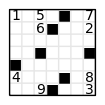

```mathematica
f[({{0, 4, 0, 1}, {9, 0, 6, 5}, {3, 8, 2, 7}}),1,4,1,2,4]
```

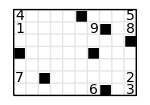

```mathematica
f[Map[Reverse,({{4, 1, 7, 0}, {0, 9, 0, 6}, {5, 8, 2, 3}})],1,4,1,6,3]
```

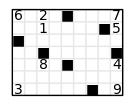

```mathematica
f[({{3, 0, 0, 6}, {0, 8, 1, 2}, {9, 4, 5, 7}}),2,3,1,2,6]
```

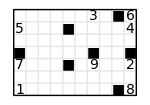

```mathematica
f[({{1, 7, 5, 0}, {0, 9, 0, 3}, {8, 2, 4, 6}}),2,3,1,6,3]
```

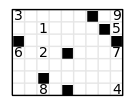

```mathematica
f[({{0, 6, 0, 3}, {8, 2, 1, 0}, {4, 7, 5, 9}}),3,2,1,2,6]
```

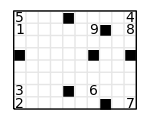

```mathematica
f[Reverse[({{7, 0, 8, 4}, {0, 6, 9, 0}, {2, 3, 1, 5}})],1,5,1,6,3]
```

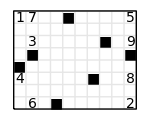

```mathematica
f[({{0, 4, 0, 1}, {6, 0, 3, 7}, {2, 8, 9, 5}}),2,3,2,1,8]
```

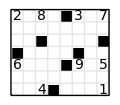

```mathematica
ff[({{0, 4, 0, 1}, {6, 0, 9, 5}, {2, 8, 3, 7}}),2,3,2,2,4]
```

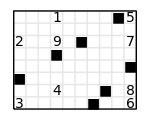

```mathematica
f[Map[Reverse,({{0, 2, 0, 3}, {1, 9, 4, 0}, {5, 7, 8, 6}})],1,4,2,3,6]
```

```mathematica
A=Permutations[Range[9]];
```

```mathematica
balhor[L_]:=Module[{},total=-L[[1]]x+L[[3]]y+L[[4]](y+z);Mod[total,L[[1]]+L[[2]]+L[[3]]+L[[4]]]==0&&total=!=0&&total=!=(L[[1]]+L[[2]]+L[[3]]+L[[4]])y]
```

```mathematica
balver[L_]:=Module[{},total=-L[[1]]a+L[[3]]b;Mod[total,L[[1]]+L[[2]]+L[[3]]]==0&&total=!=0]
```

```mathematica
place={{{1},{1},{5}},{{1},{1},{6}},{{1},{1},{9}},{{1},{1},{10}},{{1},{2},{4}},{{1},{2},{6}},{{1},{2},{8}},{{1},{2},{10}},{{1},{3},{4}},{{1},{3},{8}},{{2},{2},{3}},{{2},{2},{7}},{{3},{4},{4}},{{4},{4},{4}},{{2},{4},{5}},{{4},{4},{5}},{{2},{4},{6}},{{1},{5},{5}}};
```

161

242

251

323

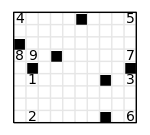

332

341

413

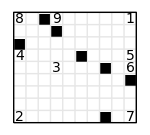

422

431

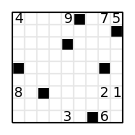

512

521

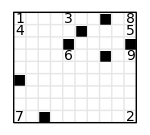

611

171

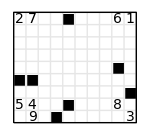

252

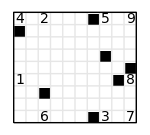

261

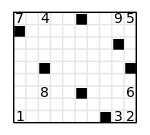

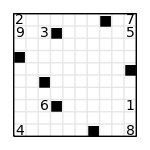

333

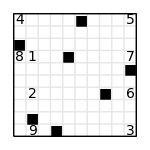

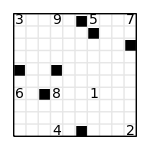

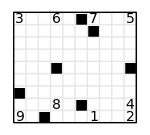

342

-Graphics-

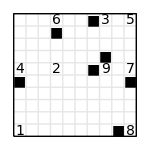

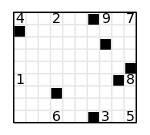

351

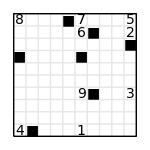

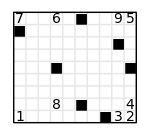

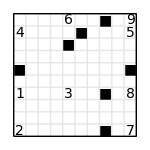

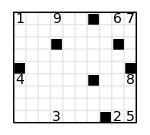

414

423

432

441

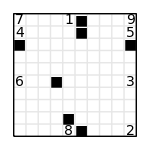

513

522

531

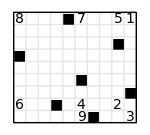

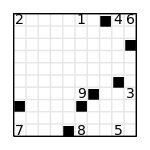

612

621

711

```mathematica
For[t=8,t≤9,t++,
For[x=1,x≤t-2,x++,
For[y=1,y≤t-x-1,y++,
z=t-x-y;
If[z<=x,Print[x,y,z];
For[kk=1,kk≤18,kk++,
For[k=1,k≤Length[A],k++,
B=Partition[Insert[A[[k]],0,place[[kk]]],4,4];
If[balhor[B[[1]]]&&balhor[B[[2]]]&&balhor[B[[3]]],
For[tt=3,tt≤9,tt++,
For[a=1,a≤tt-1,a++,
b=tt-a;
BT=Transpose[B];
If[balver[BT[[1]]]&&balver[BT[[2]]]&&balver[BT[[3]]]&&balver[BT[[4]]],
Print[f[B,x,y,z,a,b]];Print[ff[B,x,y,z,a,b]];
]]]]]]]]]]
```

```mathematica
place={{{1},{5},{9}},{{1},{5},{10}},{{1},{6},{8}},{{1},{7},{8}},{{1},{7},{9}},{{2},{4},{9}}};
```

-Graphics-

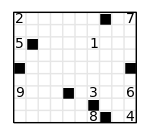

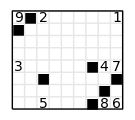

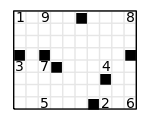

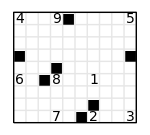

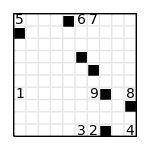

```mathematica
For[t=4,t≤9,t++,
For[x=1,x≤t-2,x++,
For[y=1,y≤t-x-1,y++,
z=t-x-y;
If[z<=x,Print[x,y,z];
For[kk=1,kk≤6,kk++,
For[k=1,k≤Length[A],k++,
B=Partition[Insert[A[[k]],0,place[[kk]]],4,4];
If[balhor[B[[1]]]&&balhor[B[[2]]]&&balhor[B[[3]]],
For[tt=3,tt≤9,tt++,
For[a=1,a≤tt-1,a++,
b=tt-a;
BT=Transpose[B];
If[balver[BT[[1]]]&&balver[BT[[2]]]&&balver[BT[[3]]]&&balver[BT[[4]]],
Print[f[B,x,y,z,a,b]];Print[ff[B,x,y,z,a,b]];
]]]]]]]]]]
```

```mathematica
balhor[L_]:=Module[{},total=-L[[1]]x+L[[3]]y;Mod[total,L[[1]]+L[[2]]+L[[3]]]==0&&total=!=0]
```

```mathematica
ff[L_,xx_,yy_,aa_,bb_]:=Module[{xxx,yyy},
xxx=xx+yy+1;yyy=aa+bb+1;Print[xx,yy,aa,bb];
hd={0,xx,xx+yy};
vd={0,aa,aa+bb};Graphics[{GrayLevel[.9],Table[Line[{{i,0},{i,yyy}}],{i,1,xxx}],Table[Line[{{0,i},{xxx,i}}],{i,1,yyy}],Black,Line[{{0,0},{xxx,0},{xxx,yyy},{0,yyy},{0,0}}],
MapIndexed[If[#1>0,te[#1,1+hd[[#2[[2]]]],1+vd[[#2[[1]]]]],{}]&,L,{2}],
MapIndexed[te["■",1+#1.hd/Total[#1],1+vd[[#2[[1]]]]]&,L,1],
MapIndexed[te["■",1+hd[[#2[[1]]]],1+#1.vd/Total[#1]]&,Transpose[L],1]
},ImageSize->15{xxx,yyy}]]
```

1 11

2 10

3 9

3948

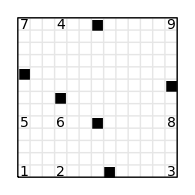

3935

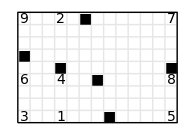

4 8

4839

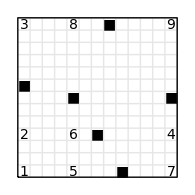

```mathematica
For[t=12,t≤12,t++,
For[x=1,x≤t/2,x++,
y=t-x;Print[x," ",y];
For[k=1,k≤Length[A],k++,
B=Partition[A[[k]],3,3];
If[balhor[B[[1]]]&&balhor[B[[2]]]&&balhor[B[[3]]],
For[tt=3,tt≤t,tt++,
For[a=1,a≤tt/2,a++,
b=tt-a;
BT=Transpose[B];
If[balver[BT[[1]]]&&balver[BT[[2]]]&&balver[BT[[3]]],
Print[ff[B,x,y,a,b]];
]]]]]]]
```

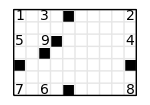

-Graphics-

-Graphics-

4 5

```mathematica
old
```